## Numerically maximising the ELBO

AUXILIARY FUNCTIONS

```mathematica
(*Binary entropy*)
H[x_]:=-x*Log[x]-(1-x)*Log[1-x]
H[0]=0;
H[1]=1;
(*General quadratic form*)
Quad[M_, a_, b_] :=a.M.b
(*Generalized Rayleigh quotient*)
raygh[A_, B_,a_,b_]:= Quad[A,a,b]/Quad[B,a,b]
```

GRAPH

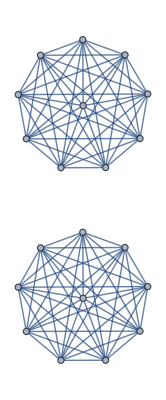

```mathematica
n= 20; (*Number of nodes*)
J= ConstantArray[1, {n, n}]-IdentityMatrix[n];
gamma1=1;
gamma2=1;
shift=0;
adj1 = AdjacencyMatrix[RandomGraph[BernoulliGraphDistribution[n/2+shift,gamma1]]];
adj2 = AdjacencyMatrix[RandomGraph[BernoulliGraphDistribution[n/2-shift,gamma2]]];
(*Block matrices*)
block[arr1_, arr2_]:=ArrayFlatten[{{arr1, ConstantArray[0, {n/2+shift,n/2-shift}]},{ConstantArray[0, {n/2-shift,n/2+shift}], arr2}}]
A=block[adj1, adj2];
graph=AdjacencyGraph[A]
Deg=DiagonalMatrix[Total[A]];
edges=Total[Total[Deg]]/2;
L=Inverse[Sqrt[Deg]].A.Inverse[Sqrt[Deg]];
```

OPTIMIZATION

```mathematica
(* -ELBO to minimize*)
(*n*H[Total[v]/n]-Total[H/@v]+*)
objective[v_]:=0.5*Quad[J, v, v] *H[raygh[A,J,v, v]]+0.5*Quad[J,1-v, 1-v]*H[raygh[A,J,1-v, 1-v] ]+Quad[J,v, 1-v]*H[raygh[A,J,v, 1-v]]
```

```mathematica
Clear[v];
v=Array[Subscript[x,#]&,n];
Minimize[{objective[v], 0<=v<=1},v]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{123.161,{x_1→1.,x_2→0.928596,x_3→0.809545,x_4→1.,x_5→0.581921,x_6→0.994284,x_7→0.349067,x_8→0.831042,x_9→0.896708,x_10→0.829511,x_11→0.304543,x_12→0.297724,x_13→0.220533,x_14→0.250378,x_15→0.,x_16→0.345463,x_17→0.115679,x_18→0.273498,x_19→0.85744,x_20→0.0772389}}

PLOTS

```mathematica
(*Objective as a function of tau*)
Plot3D[
objective[
Flatten[{ConstantArray[1/2,n/2],ConstantArray[1/2,-2+n/2],a,b}]],
{a,0,1},{b,0,1},ColorFunction->"TemperatureMap",PlotTheme->"Detailed",PlotLegends->None
]
```

-Graphics3D-

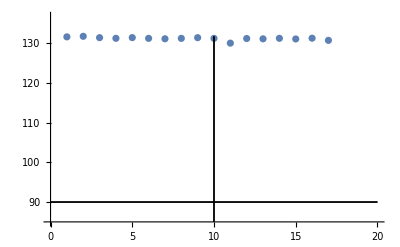

Minimum in list: 130.041 at n=11

Objective at tau1: 90.

Objective at tau2: 90.

Objective at tauComplete: 131.435

```mathematica
(*Objective on vertices as a function of ntau*)
Clear[rv,objlist,tauL1,tauL2,maxy,miny];
tauL1=Flatten[{ConstantArray[1,n/2+shift],ConstantArray[0,n/2-shift]}];
tauL2=Flatten[{ConstantArray[0,n/2+shift],ConstantArray[1,n/2-shift]}];
tauComplete =ConstantArray[1-0.01,n];
rv=Table[RandomSample[Flatten[{ConstantArray[1,i],ConstantArray[0,n-i]}]],{i,2,n-2}];
objlist=objective/@rv;
maxy=Max[objlist];
miny=Min[Min[objlist],objective[tauL1],objective[tauL2]];
ListPlot[objlist,PlotRange->{{0,n},{miny-5,maxy+5}},
Epilog->{
Line[{{n/2 +shift,miny-5},{n/2 +shift,maxy}}],
Line[{{n/2 -shift,miny-5},{n/2 -shift,maxy}}],
Line[{{0,objective[tauL1]},{n,objective[tauL1]}}],
Line[{{0,objective[tauL2]},{n,objective[tauL2]}}]
} ](*Objective function on our suspected solutions*)
Print["Minimum in list: ", Min[objlist], " at n=", Part[Ordering[objlist],1]]
Print["Objective at tau1: ",objective[tauL1]]
Print["Objective at tau2: ",objective[tauL2]]
Print["Objective at tauComplete: ",objective[tauComplete]]
```

```mathematica
(*Objective function along diagonals*)
extra=10;
tauL=Flatten[{ConstantArray[0,n/2-extra],ConstantArray[1,n/2+extra]}]; (*Use RandomSample to shuffle*)
Plot[objective[a *tauL+(1-a)*(1-tauL)],{a,0,1}]
```

-Graphics-

```mathematica
(*Objective as a function of edges, merely interesting*)
Clear[τ]
c=Binomial[n,2];
ntau=20;
Ctau=Binomial[ntau,2];
Ctaubar=Binomial[n-ntau,2];
Cm=ntau*(n-ntau);
f[x_,y_]:= n*H[ntau/n]+Ctau*H[x/Ctau]+Ctaubar*H[y/Ctaubar]+Cm*H[(edges-x-y)/Cm]
Plot3D[f[x,y],{x,0,Ctau},{y,0,Ctaubar}, RegionFunction->Function[{x,y},x+y<=edges]]
```

Plot3D::plld: Endpoints for y in {y,0,0} must have distinct machine-precision numerical values.

Plot3D[f(x,y),{x,0,Ctau},{y,0,Ctaubar},RegionFunction→({x,y}↦x+y≤edges)]

Some interesting test cases:

Two complete components of same size.

```mathematica
n= 40; (*Number of nodes*)
gamma1=1;
gamma2=1;
shift=0;
```

Two complete components of different but comparable size

```mathematica
n= 40; (*Number of nodes*)
gamma1=1;
gamma2=1;
shift=10;
```

These two seem to show that our intuition for the optimal τ only works for cases where each community has the same size.

Two complete components of very different size

```mathematica
n= 40; (*Number of nodes*)
gamma1=1;
gamma2=1;
shift=15;
```

In this case, in the plot of the objective function across half of the cube you can see explicitly that the objective function is not convex. The plot as a function of nτ shows clearly that our intuition fails.